## Orbital Plot from Cube Format Import & Interpolation

#### Copyright, License, relevant Literature

© 2024 Jochen Autschbach

Literature: 

[1] Pierpaolo Morgante & Jochen Autschbach, Molecular Orbitals, American Chemical Society, Washington, DC, 2023.

See file LICENSE in https://github.com/jautschbach/mathematica-notebooks for license information and disclaimers.

If you use this notebook, or code based on it, for your own research, please cite the textbook reference [1]  and provide the URL from where you obtained this notebook.

#### Initialization cells

```mathematica
SetDirectory[NotebookDirectory[]];
colors = {
ColorData["RedBlueTones",0.05],
ColorData["RedBlueTones",0.80],
ColorData["GreenPinkTones",0.15],
ColorData["SolarColors",0.95]
};
vp=ViewPoint/.Options[Graphics3D]; 
vv=ViewVertical/.Options[Graphics3D];
customImporter[path_]:=Block[{textmol,goodmol},
mol=Import[path,"Molecule"];
textmol=ToString[InputForm[mol]];
goodmol=ToExpression@StringReplace[textmol,
{"\"Double\""->"\"Single\"","\"Triple\""->"\"Single\"","\"Aromatic\""->"\"Single\"","]" ~~ EndOfString -> ", ValenceFilling->None]"}];
Return[goodmol]
];
```

#### Make a list of cube files from the current directory (use ⇧+⌤ to evaluate cells after placing cursor in them).

```mathematica
ext = "cube";
flist = FileNames["*."<>ext];
n = Length[flist];
TableForm[flist,TableHeadings->{Range[n],{}}, , TableAlignments->Left]
```

1 | example.cube

#### Pick cube to plot

Pick one  cube that we will work with, and assign a scaling factor different from 1 if you need

```mathematica
pick = 1;
scale = 1; (* probably best to leave this as-is *)
```

#### Check what’s in the cube

Available PlotThemes are:HeavyAtom,BallAndStick,SpaceFilling,Tubes,Wireframe

```mathematica
plottheme="Tubes";
mol = customImporter[flist[[pick]]];
molplot = MoleculePlot3D[mol, PlotTheme->plottheme];Import[flist[[pick]],"Graphics3D",PlotTheme->plottheme,"InferBondTypes"->False,AtomLabels->"AtomIndex"]
```

-Graphics3D-

```mathematica
points = QuantityMagnitude @ mol["AtomCoordinates"]; TableForm[points,  TableHeadings->{Range[Length[points]],{}}, , TableAlignments->Left ]
```

|  |  | 
1 | 0. | 0. | 1.76
2 | 0. | 0. | 0.
3 | 0. | 0. | -1.76

#### Create Interpolation function f[x,y,z]

```mathematica
Block[{cube, vol, volRange,data,n, min, max, step},
cube=flist[[pick]];
vol = Import[cube,"VolumetricData"];
volRange = vol["DataRange"];
data = Normal[vol[["Data",1]]];
n = Dimensions[data];
min = Table[volRange[[i,1]],{i,1,3}];
max = Table[volRange[[i,2]],{i,1,3}];
step = {
(max[[1]]-min[[1]])/(n[[3]]-1),
(max[[2]]-min[[2]])/(n[[2]]-1),
(max[[3]]-min[[3]])/(n[[1]]-1)
};

Print["Cube min(x,y,z) and max(x,y,z): ", min, ",  ", max];

(* Now we make an interpolation function from the 3D volume data, so we can plot slices easier
(note the use of data[[z,y,x]] below, and the gymnastics with n[[i]] in the "step" array above,which is because the z-loop runs fastest in the cube specification's Fortran code) *)

Clear[f];
f = Interpolation[Flatten[Table[{
min[[1]] + (x-1) step[[1]],
min[[2]] + (y-1) step[[2]],
min[[3]] + (z-1) step[[3]],
scale * data[[z,y,x]]
},{x,1,n[[3]]},{y,1,n[[2]]},{z,1,n[[1]]}],2]];

];
```

Cube min(x,y,z) and max(x,y,z): {-3.77622,-3.77622,-3.77622},  {3.77624,3.77624,3.77624}

#### Plot the data

Here, we now have a large number of options to plot the data. Everything we need is in the interpolation function f[x,y,z].
Mathematica should give errors when plots go outside of the interpolation range, but that does not always happen, it seems.
Therefore, make sure your plot ranges don’t exceed the cube dimensions from the output of the prev. input cell (Angstrom units)

For examples how to fancy-up the plots, see, for example the Chapter 4 supplement for download on thi spage:
https://ja01.chem.buffalo.edu/in-focus-mo-ebook/in-focus-mo-ebook.html

The example data set is for an atomic orbital centered on atom 2 at (0,0,0). Let’s plot the radial function R (in this case, R is proportional to the function along the z-axis)

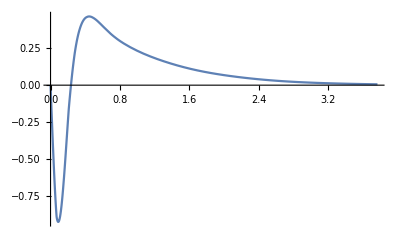

```mathematica
Plot[f[0,0,z],{z,0,3.77},PlotRange->All]
```

Plot the radial density R^2 r^2 (for the selected orbital this is up to a constant factor the orbital square times z^2 along the z coordinate)

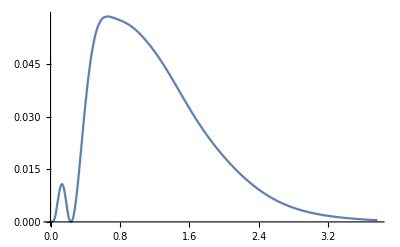

```mathematica
Plot[f[0,0,z]^2 z^2,{z,0,3.77},PlotRange->All]
```

Make a 2D contour line plot in the xz plane:

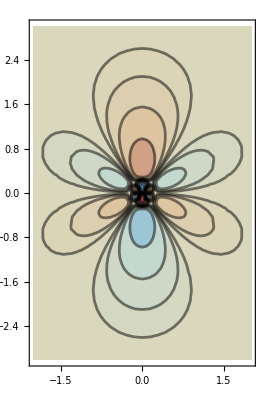

```mathematica
With[{r=0.03,j=6, base = 2},
contours=Flatten[{Table[r  base^n,{n,0,j}],Table[-r 2^n,{n,0,j}]}
]];
col[f_] := ColorData["RedBlueTones",1-f];
ContourPlot[f[x,0,z],{x,-2,2},{z,-3,3},PlotRange->All,Contours->contours,AspectRatio->Automatic,
ColorFunction->col,ContourStyle->Thickness[0.005]]
```